```mathematica
Needs["PlotLegends`"]
SetDirectory["/home/quiddi/NetBeansProjects/sub_2222/ausgabe/"]
m1:=Import["density_Eisen","CSV"]
m2:=Import["density_Sauerstoff","CSV"]
m3:=Import["density_Proteobacteria","CSV"]
m4:=Import["density_Methan","CSV"]
m5:=Import["density_Cyanobakterien","CSV"]
m6:=Import["density_Sauerstoff_total","CSV"]
```

/home/quiddi/NetBeansProjects/sub_2222/ausgabe

```mathematica
x1:=ListPlot[{m1,m2,m3,m4,m5,m6},Joined->True,PlotRange->{{0,2000},{0,1}},PlotLegend->{"Iron","Oxygen","Proteob.","Methan","Cyanob.","Oxygen A."},LegendPosition->{0.8,-0.8},AxesLabel->{"Timesteps","Concentration"},PlotStyle->{Blue,Orange,Green,Red,Purple,Directive[Dashed,Green]}]
Export["density.pdf",x1]
```

density.pdf

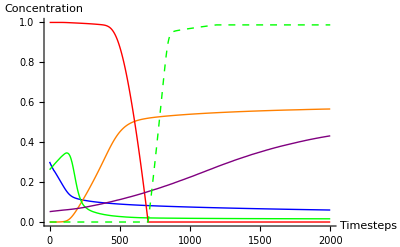

```mathematica
x1
```